# The Energy Function of ^163 Lu

## A quantitative study on the evolution of numerical values of ℋ w.r.t. the spherical coordinates and “free” terms

## ℋ=I/2(A_1+A_2)+A_3 I^2+I(I-1/2)sin^2 θ(A_1 cos^2 φ+A_2 sin^2 φ-A_3)+j/2(A_2+A_3)+A_1 j^2-2 A_1 Ij sinθ-V(2j-1)/(j+1)sin(γ+π/6);

## T0=free term

## T1=mixed term f(θ,φ)

## T2=theta term g(θ)

```mathematica
IF[i_]:=1/(2i);
t0[I_,j_,a1_,a2_,a3_,V_,γ_]:=I/2(a1+a2)+a3*I^2+j/2(a2+a3)+a1*j^2-V(2j-1)/(j+1)Sin[γ+π/6];
t1[I_,a1_,a2_,a3_,θ_,φ_]:=I(I-1/2)Sin[θ]^2(a1*Cos[φ]^2+a2*Sin[φ]^2-a3);
t2[I_,j_,a1_,θ_]:=-2*a1*I*j*Sin[θ];
```

## Study each term

### Spins & constants

```mathematica
spin1=25/2;
spin2=31/1;
spin3=37/2;
spin4=51/2;
j=13/2;
i1Fit=73;
i2Fit=3;
i3Fit=67;
vFit=6.01;
```

## T_0 - evolution with γ

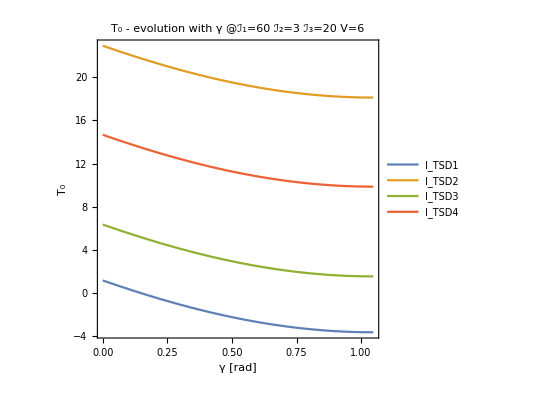

```mathematica
p1[i1_,i2_,i3_,v_]:=Plot[{t0[spin1,j,IF[i1],IF[i2],IF[i3],v,gm],t0[spin2,j,IF[60],IF[3],IF[20],v,gm],t0[spin3,j,IF[i1],IF[i2],IF[i3],v,gm],t0[spin4,j,IF[i1],IF[i2],IF[i3],v,gm]},{gm,0,π/3},Frame->True,Axes->False,FrameLabel->{"γ [rad]","T_0"},FrameStyle->Directive[Black,Thick],LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},AspectRatio->1,PlotLegends->{"I_TSD1","I_TSD2","I_TSD3","I_TSD4"},PlotLabel->StringTemplate["T_0 - evolution with γ \n @ℐ_1=`` ℐ_2=`` ℐ_3=`` V=``"][i1,i2,i3,v]];
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Reports/T0_gm.jpeg",p1[60,3,20,6]];
Show[p1[60,3,20,6]]
```

## T_0 - evolution with V

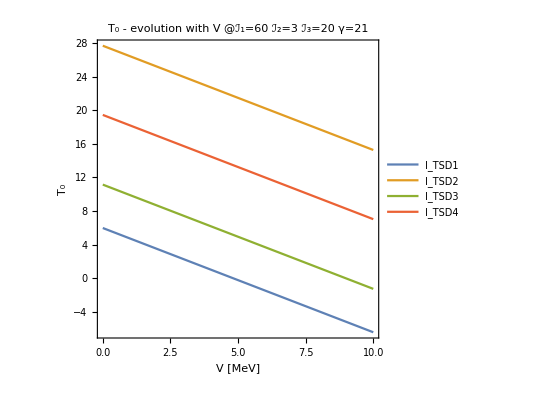

```mathematica
p2[i1_,i2_,i3_,gm_]:=Plot[{t0[spin1,j,IF[i1],IF[i2],IF[i3],v,gm*π/180],t0[spin2,j,IF[i1],IF[i2],IF[i3],v,gm*π/180],t0[spin3,j,IF[i1],IF[i2],IF[i3],v,gm*π/180],t0[spin4,j,IF[i1],IF[i2],IF[i3],v,gm*π/180]},{v,0,10},Frame->True,Axes->False,FrameLabel->{"V [MeV]","T_0"},FrameStyle->Directive[Black,Thick],LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},AspectRatio->1,PlotLegends->{"I_TSD1","I_TSD2","I_TSD3","I_TSD4"},PlotLabel->StringTemplate["T_0 - evolution with V \n @ℐ_1=`` ℐ_2=`` ℐ_3=`` γ=``"][i1,i2,i3,gm]];
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Reports/T0_V.jpeg",Show[p2[60,3,20,21]]];
Show[p2[60,3,20,21]]
```